```mathematica
(* Radiative Quenching, Chapter 3 *)
(* This one uses my paper *)

(*electron mass *)
Subscript[m, e]=1;
(* Proton Mass *)
Subscript[m, p]=1836;
(* Reduced Mass *)
μ=Subscript[m, p]/2;
hbar= 1;  
hbarSI =1.054571817*^-34;
cLight=137.036 ;(*SpeedOfLight, atomic units*)
cLightSI= 299792458 ;(*SpeedOfLight, m/s*)
oneSec = 2.418884326509*^-17;  (* 1 sec SI <-> 1 sec AU *)
aBorh = 5.29177*^-11;   (* Si <-> AU *)

(* RawData format R,E, E + 1/R,A,p *)

vSg1RawData = Import["/Users/zelimir/Work/Physics-Thesis/thesis-2/ZelimirOverleaf/MathematicaCodeFinal/gerade1sV3.mx"];
vSu2RawData = Import["/Users/zelimir/Work/Physics-Thesis/thesis-2/ZelimirOverleaf/MathematicaCodeFinal/ungerade1sV3.mx"];


vSg1Data =vSg1RawData[[1;;44]];
vSu2Data = vSu2RawData[[1;;44]];

(* Calculate the Transition Dipole Moment *)
(* Upper Limit for integration *)
maxR = vSg1Data[[Length[vSg1Data]]][[1]];
Print["maxR=",maxR]
maxR = 20;
maxIndex = 40;

Print["R=",vSg1Data[[maxIndex,1]], ", A=",vSg1Data[[maxIndex,4]],", p=", vSg1Data[[maxIndex,5]]];
Print["R=",vSu2Data[[maxIndex,1]], ", A=",vSu2Data[[maxIndex,4]],", p=", vSu2Data[[maxIndex,5]]];
```

maxR=31

R=27, A=511764., p=27.1889

R=27, A=210927., p=27.2254

0.00074606

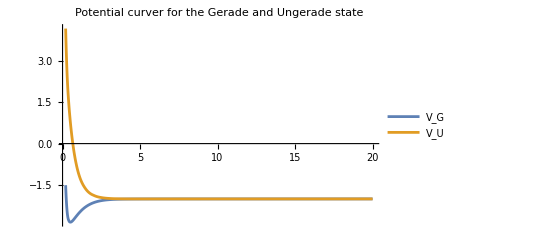

```mathematica
(* Load Potential curves for 1sg, 2sg states 
"R,E, E + 1/R,A,p *)
(* 1sg state, potential curve *)
vG=Interpolation[Transpose[{vSg1Data[[All,1]],vSg1Data[[All,3]]}], InterpolationOrder->3];
(* 2sg state, potential curve *)
vU=Interpolation[Transpose[{vSu2Data[[All,1]],vSu2Data[[All,3]]}], InterpolationOrder->3];

deltaV[r_]:=Abs[vG[r]-vU[r]];
deltaV[20]
Plot[{vG[r],vU[r]},{r,0.2,maxR}, PlotRange->Full, PlotLegends->{"V_G","V_U"}, PlotLabel->"Potential curver for the Gerade and Ungerade state"]
```

```mathematica
(* Compute the Dipole momement D(r) for the single value of R *)
singleDR[R_,a1_,p1_,a2_,p2_, maxDistance_]:=Module[{norm1, norm2,dInt, l1,l2,m1,m2,lmNorm1, lmNorm2},
(* 1s wavefunction *)
l1=NDSolveValue[{(ξ^2-1)L''[ξ]+ξ * L'[ξ]+ (a1 +2 R ξ -p1^2 ξ^2)L[ξ]==0 ,L[1.001]==0,L'[1.001]==1 },L,{ξ,1.001,maxDistance}];
m1=NDSolveValue[{(1-η^2)M''[η]-η *M'[η] - (-a1 + p1^2 η^2)M[η]==0, M[-0.999]==0,M'[-0.999]==1}, M,{η,-.999,.999}];
m1 = NDEigensystem[{(1-η^2)M''[η]-η *M'[η] - (-A + p1^2 η^2)M[η]/. {R->1,A->a1},H[-1]==0,H[1]==0,H'[0]==0},M[η],{η,-.999,999},3];

(* 2s wavefunction *) 
l2=NDSolveValue[{(ξ^2-1)L''[ξ]+ξ * L'[ξ]+ (a2+2 R ξ -p2^2 ξ^2)L[ξ]==0 ,L[1.001]==0,L'[1.001]==1 },L,{ξ,1.001,maxDistance}];
m2=NDSolveValue[{(1-η^2)M''[η]-η *M'[η] - (-a2 + p2^2 η^2)M[η]==0, M[-0.999]==0,M'[-0.999]==1}, M,{η,-.999,.999}];

Print["R=",R];
(* Compute <ψ|ψ> = <Subscript[ψ, 1s]|Subscript[ψ, 1s]> + <Subscript[ψ, 2s]|Subscript[ψ, 2s]> *)
(* <Subscript[ψ, 1s]|Subscript[ψ, 1s]> *)
norm1=Sqrt[NIntegrate[Abs[l1[ξ] m1[η]]^2,{η,-.999,.999},{ξ,1.001,maxDistance}]];
(* <Subscript[ψ, 2s]|Subscript[ψ, 2s]> *)
norm2=Sqrt[NIntegrate[Abs[l2[ξ]m2[η]]^2,{η,-.999,.999},{ξ,1.001,maxDistance}]];

lmNorm1[ξ_,η_]:=1/norm1 l1[ξ]m1[η];
lmNorm2[ξ_,η_]:=1/norm2 l2[ξ]m2[η];

dInt=(R/2)^3 NIntegrate[Conjugate[lmNorm1[ξ,η]]ξ η lmNorm2[ξ,η]((ξ^2-η^2)/(√(ξ^2-1)√(1-η^2))),{η,-0.999,0.999},{ξ,1.001,maxDistance}];
{R,dInt }
];

singleDR[vSg1Data[[24]][[1]],vSg1Data[[19]][[4]],vSg1Data[[19]][[5]],vSu2Data[[19]][[4]],vSu2Data[[19]][[5]],5]
(*singleDR[vSg1Data[[14]][[1]],vSg1Data[[19]][[4]],vSg1Data[[19]][[5]],vSu2Data[[19]][[4]],vSu2Data[[19]][[5]],5]
singleDR[vSg1Data[[15]][[1]],vSg1Data[[20]][[4]],vSg1Data[[20]][[5]],vSu2Data[[20]][[4]],vSu2Data[[20]][[5]],5]*)
```

```mathematica
(* Get all Rs, and coefficients A and p and calculate D(R) for all Rs *)
(* RawData format R,E, E + 1/R,A,p *)
inputData = Transpose[{vSg1Data[[1;;maxIndex,1]],vSg1Data[[1;;maxIndex,4]],vSg1Data[[1;;maxIndex,5]],vSu2Data[[1;;maxIndex,4]],vSu2Data[[1;;maxIndex,5]]}];

allDR =Map[singleDR[#[[1]],#[[2]],#[[3]],#[[4]],#[[5]], maxR] &, inputData];
```

R=0.2

R=0.3

R=0.4

R=0.5

R=0.6

R=0.7

R=0.8

R=0.9

R=1.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

R=1.1

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

R=1.5

R=2.

R=2.5

R=3.

R=3.5

R=4.

R=4.5

R=5.

General::munfl: 1/(5.21659×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/(6.09014×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/(7.11013×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

R=6

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.3263282948944883540357077666577435948478247042233900141812762618×10^1022 and 2.2070702173373638426065880761956358430445405697173175264431359432×10^1017 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.8193135995668147837463173514400255226806955497669077944891225638×10^1175 and 7.1660645711250950570297279089793088794970936759139185845352659856×10^1170 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

R=7

R=8

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.7884087902962610400009512331396872688629835609845793927698428452×10^1177 and 1.4206317681954839100756898518203933243237359024823787711730228212×10^1173 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

R=9

R=10

R=11

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

R=12

R=13

R=14

R=15

R=16

R=17

R=18

R=19

R=20

R=21

R=22

R=23

R=24

R=25

R=26

R=27

```mathematica
allDR // MatrixForm
```

(0.2 | -0.0893696
0.3 | -0.13213
0.4 | -0.384232
0.5 | 0.0254169
0.6 | -0.406694
0.7 | 1.78895
0.8 | 0.522647
0.9 | -1.98178
1. | -1.3272
1.1 | -9.10647
1.5 | -45.9815
2. | -133.675
2.5 | -211.581
3. | -532.668
3.5 | -106.561
4. | 827.81
4.5 | 1550.91
5. | 137.769
6 | 594.81
7 | -22947.6
8 | -36928.8
9 | -53711.6
10 | -74750.3
11 | -5020.49)

{{0.2,-5.51836×10^-30},{0.3,-6.06937×10^-30},{0.4,6.34428×10^-30},{0.5,-1.56475×10^-28},{0.6,-4.59063×10^-28},{0.7,-7.99027×10^-28},{0.8,1.08538×10^-27},{0.9,-1.16717×10^-27},{1.,2.80203×10^-28},{1.1,-8.39946×10^-28},{1.5,-8.00093×10^-27},{2.,4.98235×10^-26},{2.5,-4.14085×10^-26},{3.,1.74667×10^-25},{3.5,-2.80807×10^-25},{4.,-2.31107×10^-25},{4.5,-6.08488×10^-25},{5.,-4.91204×10^-25},{6,0.},{7,1.09188×10^-24},{8,0.},{9,-5.86479×10^-24},{10,8.2292×10^-24},{11,0.},{12,0.},{13,0.},{14,0.},{15,0.},{16,0.},{17,0.},{18,0.},{19,0.},{20,0.},{21,0.},{22,0.},{23,0.},{24,0.},{25,0.},{26,0.},{27,0.}}

InterpolatingFunction::dmval: Input value {0.100141} lies outside the range of data in the interpolating function. Extrapolation will be used.

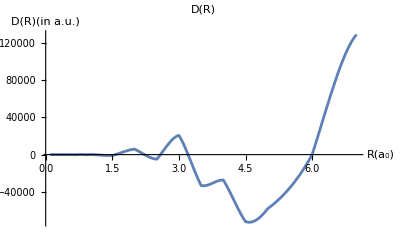

InterpolatingFunction::dmval: Input value {0.100407} lies outside the range of data in the interpolating function. Extrapolation will be used.

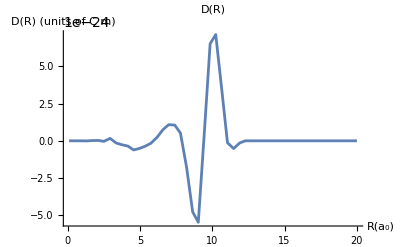

```mathematica
(* Dipole moment in SI units *)
drAUtoSI = 8.478*^-30; (* Cm *)
allDRSI=allDR;
allDRSI[[All,2]] =allDR[[All,2]]*drAUtoSI;
allDRSI

dR =Interpolation[Transpose[{allDR[[All,1]],allDR[[All,2]]}], InterpolationOrder->3];
Plot[dR[r],{r,0.1, 7}, PlotLabel->"D(R)", AxesLabel->{"R(a_0)", "D(R)(in a.u.)"}, PlotRange->Full]

dRSI =Interpolation[Transpose[{allDRSI[[All,1]],allDRSI[[All,2]]}], InterpolationOrder->3];
Plot[dRSI[r],{r,0.1, maxR}, PlotLabel->"D(R)", AxesLabel->{"R(a_0)", "D(R) (units of C m)"}, PlotRange->Full, Axes->True]
```

InterpolatingFunction::dmval: Input value {0.100202} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

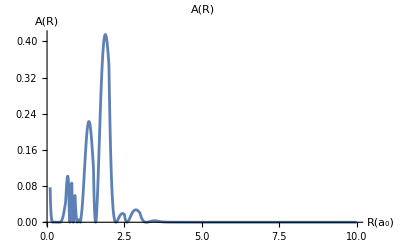

InterpolatingFunction::dmval: Input value {0.100202} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

InterpolatingFunction::dmval: Input value {0.100202} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

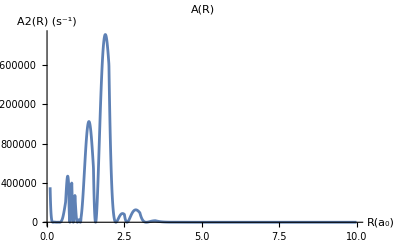

```mathematica
aR[R_]:=4/(3hbar cLight^3)(dR[R])^2((vU[R]-vG[R])/hbar)^3;

aRAUtoSI = 4.1341*^16;
aRSI[R_]:=aR[R]*aRAUtoSI;

aRSI2[R_]:=4/(3 hbarSI cLightSI^3)(dRSI[R])^2(((vU[R]-vG[R])4.35974*^-18)/hbarSI)^3;


Plot[aR[r],{r,.1,  10}, PlotLabel->"A(R)", AxesLabel->{"R(a_0)", "A(R)"}, PlotRange->Full]
Plot[aRSI[r],{r,.1,  10}, PlotLabel->"A(R)", AxesLabel->{"R(a_0)", "A(R) (s^-1)"}, PlotRange->Full]
Plot[aRSI2[r],{r,.1,  10}, PlotLabel->"A(R)", AxesLabel->{"R(a_0)", "A2(R) (s^-1)"}, PlotRange->Full]
```